# Outer Products for Matrix Multiplication

## Technical Report, GSI Technology

Brian Beckman
Technology Fellow
November, 2023

## Abstract

Accumulated outer products are much faster than iterated inner products for matrix multiplication.

## Iterated Inner Product Versus Accumulated Outer Product

### Set Up

Set some array dimensions as mutually co-prime numbers, for generality.

Consider a small matrix of floating-point numbers in the range [0., 1.], inclusive both ends.

```mathematica
ClearAll[m,n,k,A,B];
m=5;k=4;n=7;GCD[m,k,n]
(A=RandomReal[{0.,1.},{m,k}])//MatrixForm
```

1

(0.221629 | 0.89834 | 0.726131 | 0.987658
0.988818 | 0.255711 | 0.0386533 | 0.720607
0.0685577 | 0.790393 | 0.353325 | 0.823387
0.0437786 | 0.354845 | 0.501183 | 0.12885
0.910475 | 0.454306 | 0.889837 | 0.664789)

Natively, A is a List of rows with two levels of brackets. Indexing A yields a row vector, with only one level of brackets.

```mathematica
A[[2]]
```

{0.988818,0.255711,0.0386533,0.720607}

To get a column of A, transpose a row of the transpose. Again, the result has only one level of brackets, so its type as a column vector is implicit. It has exactly the same shape as a row vector. This ambiguity is a defect, however, it is commonplace in programming languages.

```mathematica
Aᵀ[[2]]ᵀ
```

{0.89834,0.255711,0.790393,0.354845,0.454306}

Write a couple of more explicit helper functions.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

Make another matrix to play with.

```mathematica
(B=RandomReal[{0.,1.},{k,n}])//MatrixForm
```

(0.923108 | 0.55426 | 0.993092 | 0.745936 | 0.885071 | 0.0398964 | 0.750968
0.18605 | 0.662866 | 0.146657 | 0.0443965 | 0.259685 | 0.300529 | 0.169085
0.270006 | 0.694104 | 0.385196 | 0.266563 | 0.0743926 | 0.391713 | 0.437537
0.0600413 | 0.921802 | 0.735641 | 0.816153 | 0.621162 | 0.233185 | 0.816383)

Check Mathematica’s built-in matrix product.

```mathematica
(A.B)//MatrixForm
```

(0.627083 | 2.13275 | 1.35811 | 1.20484 | 1.09696 | 0.793561 | 1.44235
1.01406 | 1.40865 | 1.56448 | 1.34738 | 1.39207 | 0.299474 | 1.39101
0.355176 | 1.56617 | 0.925817 | 0.852424 | 0.803674 | 0.570674 | 1.01192
0.24949 | 0.726127 | 0.383357 | 0.287168 | 0.248216 | 0.334753 | 0.417352
1.20517 | 2.03623 | 1.80262 | 1.47909 | 1.40295 | 0.676436 | 1.69261)

### Iterated Inner Product

Iterate inner products -- a school algorithm -- row vectors times column vectors. The following shows row 2 of A inner-product col 2 of B to produce element (2,2) of the product A.B.

```mathematica
row[A,2].col[B,2]
```

1.40865

Here is iterated inner product compared for accuracy against the built-in, intrinsic matrix product.

```mathematica
On[Assert];
```

```mathematica
Assert[Module[{i,j,ab=ConstantArray[0.0,{m,n}]},
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];
ab]===A.B]
```

### Accumulated Outer Product

Check outer product:

```mathematica
Outer[Times,col[A,2],row[B,2]]//MatrixForm
```

(0.167136 | 0.595478 | 0.131748 | 0.0398832 | 0.233285 | 0.269977 | 0.151895
0.047575 | 0.169502 | 0.0375017 | 0.0113527 | 0.0664042 | 0.0768485 | 0.0432367
0.147053 | 0.523924 | 0.115917 | 0.0350907 | 0.205253 | 0.237536 | 0.133643
0.066019 | 0.235215 | 0.0520405 | 0.0157539 | 0.092148 | 0.106641 | 0.0599989
0.0845237 | 0.301144 | 0.0666271 | 0.0201696 | 0.117977 | 0.136532 | 0.0768162)

Here is matrix product as accumulated outer product compared against the built-in, intrinsic matrix product. Notice there is only one loop, so this outer-product algorithm should be much faster than the iterated inner-product.

```mathematica
Assert[Module[{kk,ab=ConstantArray[0.0,{m,n}]},
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];
ab]===A.B]
```

### Helper Functions

Even with these very small matrices, the accumulated outer product is much faster than the iterated inner product.

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
With[{ab=builtInProduct[m,k,n,A,B],
abi=iteratedInnerProduct[m,k,n,A,B],
aba=accumulatedOuterProduct[m,k,n,A,B]},
Assert[ab["result"]===abi["result"]===aba["result"]];
Print[<|"built-in time"->ab["time"],
"inner time"->abi["time"],"outer time"->aba["time"],
"inner/outer ratio"->N[abi["time"]/aba["time"]],
"outer/built-in ratio"->N[aba["time"]/ab["time"]]|>];]
```

<|built-in time→3.×10^-6 s,inner time→0.000095 s,outer time→0.000015 s,inner/outer ratio→6.33333,outer/built-in ratio→5.|>

### Large Matrices

With the following dimensions, iterated inner product takes 20 minutes: too long to wait.

```mathematica
GCD[1001,1114,993]
```

1

```mathematica
ClearAll[timings];
(timings=With[{precision=1*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,400,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 1.×10^-6 s | 9.×10^-6 s | 7.×10^-6 s
26 | 0.000017 s | 0.001843 s | 0.00009 s
51 | 0.000016 s | 0.008124 s | 0.000237 s
76 | 0.000243 s | 0.034737 s | 0.000699 s
101 | 0.000043 s | 0.064819 s | 0.002 s
126 | 0.000142 s | 0.106089 s | 0.003443 s
151 | 0.000113 s | 0.169726 s | 0.006113 s
176 | 0.0002 s | 0.307111 s | 0.005603 s
201 | 0.000218 s | 0.452531 s | 0.008021 s
226 | 0.000264 s | 0.572586 s | 0.01064 s
251 | 0.003701 s | 0.918154 s | 0.016135 s
276 | 0.000415 s | 1.01484 s | 0.014621 s
301 | 0.002413 s | 1.37303 s | 0.026067 s
326 | 0.000525 s | 1.79057 s | 0.02843 s
351 | 0.000662 s | 1.96772 s | 0.031114 s
376 | 0.004752 s | 2.69524 s | 0.031864 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

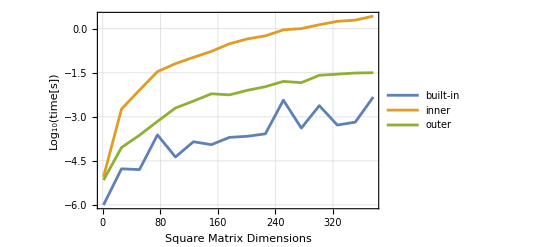

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```